-Graphics-

# The Wolfram Language: Introduction to Machine Learning

## The Neural Network Framework—Everything you need

## Learning Objectives

### What Is a Neural Network?

### The Wolfram Neural Net Repository

Location

Pre-built models

Transfer Learning

### The Wolfram Language Neural Net Framework

Building

Training

Testing

Inside a neural net

Adaptation

## Neural Networks Definition

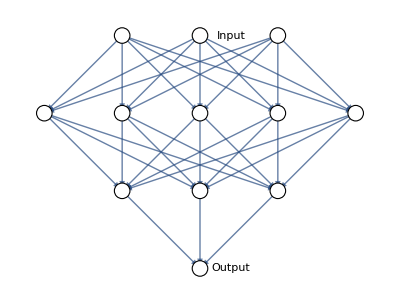

Multiple layers of fitting with increasing abstraction

Alternating linear and nonlinear layers

Special layers to target certain features: convolutional, recurrent, LSTM, etc.

## The Neural Net Repository: Location

The Wolfram Neural Net Repository has been created as a location where users can find a series of neural networks for a variety of purposes. The main idea is that any network in the repository is easy to retrieve and reuse with little user effort.

Each page detailing a neural net in the repository comes with information on its creation, architecture and training.

## How to Use the Repository

Examples in the Wolfram Neural Net Repository include Wolfram Language code showing how to retrieve and use the neural net model.

### Age Guesser

How old are you?

```mathematica
ageNM=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data"]
```

```mathematica
ageNM[-Graphics-]
```

### Image Contents Recognizer

What is the camera seeing?

```mathematica
inception=NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

```mathematica
inception[-Graphics-]
```

## Transfer Learning

Retrain the “Inception V3 Trained on ImageNet Competition Data” neural network to recognize the dog images from before.

### Retrieve and Prepare the Data

Set the image directory:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Images"}]];
```

Label the images:

```mathematica
dog1Images=Map[# -> "Chihuahua"&, Import/@Flatten[RandomSample[FileNames["*.jpg",#],100]&/@{"n02085620-Chihuahua"}]];
dog2Images=Map[# -> "Labrador_retriever"&, Import/@Flatten[RandomSample[FileNames["*.jpg",#],100]&/@{"n02099712-Labrador_retriever"}]];
```

Combine the two sets:

```mathematica
tempSet=Union[RandomSample[dog1Images,Round@(Length[dog1Images]*0.3)],RandomSample[dog2Images,Round@(Length[dog2Images]*0.3)]];
```

### Now to Separate the Prepared Data into Testing and Training Datasets

Set up the validation set for training:

```mathematica
validationSet=RandomSample[tempSet,Round@(Length[tempSet]*0.5)];
```

Set up the classifier measurements dataset:

```mathematica
cmSet=Complement[tempSet,validationSet];
```

Check for duplicates:

```mathematica
Intersection[validationSet,cmSet]
```

Set up data for training:

```mathematica
trainingSet=Complement[Union[dog1Images,dog2Images],tempSet];
```

Check for duplicates:

```mathematica
Intersection[tempSet,trainingSet]
```

```mathematica
Values@trainingSet//DeleteDuplicates
```

### Retrain

Remove the linear layer from the pre-trained net:

```mathematica
tempNet=Take[inception,{1,-4}]
```

Create a new net composed of the pre-trained net followed by a linear layer and a softmax layer:

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Chihuahua","Labrador_retriever"}}]]
```

Train on the dataset, freezing all the weights except for those in the “linearNew” layer:

```mathematica
trainedNet=NetTrain[newNet,trainingSet,LearningRateMultipliers->{"linearNew"->1,_->0},TargetDevice->"GPU"]
```

Do not forget to test it!

```mathematica
NetMeasurements[trainedNet,cmSet,"Accuracy"]
```

```mathematica
NetMeasurements[trainedNet,cmSet,"ConfusionMatrixPlot"]
```

## The Neural Net Framework: Layers

The Wolfram Language has a built in framework for handling neural networks. Part of this framework is for handling the various types of layers. This language of primitives allows you to modify and build networks:

```mathematica
?*Layer*
```

## The Neural Net Framework: Chaining Layers

Building neural networks in the Wolfram Language is made easy and simple with the use of the layer primitives.

This simple neural network has been designed to recognize written numerical digits:

```mathematica
charNetChain = NetChain[{LinearLayer[10], SoftmaxLayer[]},
  "Input" -> NetEncoder[{"Image", {28, 28}, ColorSpace -> "Grayscale"}],
  "Output" -> NetDecoder[{"Class", Range[0, 9]}]]
```

Now to initialize the network:

```mathematica
charNet=NetInitialize[charNetChain]
```

This network is ready for training and testing.

## The Neural Net Framework: Training

Key idea: Neural networks can be represented as a symbolic graph where each layer holds fixed information about the layer type, inputs and outputs and trainable weights. You can manipulate this expression like any other symbolic object. Training with data just optimizes the weights in the object:

```mathematica
data=RandomSample[ExampleData[{"MachineLearning","MNIST"},"Data"],150];
```

```mathematica
charNetTrained=NetTrain[charNet,data]
```

```mathematica
charNetTrained[-Graphics-]
```

```mathematica
charNetTrained[-Graphics-,"Probabilities"]
```

```mathematica
Row[Map[ListDensityPlot[Reverse[Partition[#,28]],PlotRange->All,Frame->False]&,Normal[NetExtract[charNetTrained,{1,"Weights"}]]]]
```

```mathematica
Normal[NetExtract[charNetTrained,{1,"Weights"}]]//Dimensions
```

## The Neural Net Framework: Testing

Each type of machine learning has its own method of testing; you cannot ask a predictor which class an image is in.

### Testing Classifiers

As usual, you get a subset of the data that the classifier has not yet seen:

```mathematica
testdata=Complement[RandomSample[ExampleData[{"MachineLearning","MNIST"},"Data"],150],data];
```

Now run the tests:

```mathematica
NetMeasurements[charNetTrained,testdata, "Accuracy"]
```

```mathematica
NetMeasurements[charNetTrained,testdata, "ConfusionMatrixPlot"]
```

## Inside a Neural Net

Key idea: The symbolic representation of a neural network is just data that can be analyzed or transformed like any other data. This means you can take a look inside to try to understand what is going on.

### Inspecting Nets

So grab the Wolfram Image Identify neural net:

```mathematica
net=NetModel["Wolfram ImageIdentify Net for WL 11.1"]
```

Its use is simple: provide an image and it identifies what it is:

```mathematica
net[-Graphics-]
```

You can easily take part of that network:

```mathematica
Take[net,10]
```

Then you can see what it is doing up to that point. In this case, each image is the neural net looking for particular features where the white parts are a positive match to part of the image. It is a combination of all these matching attempts that allows the neural net to determine what it is looking at:

```mathematica
Image/@Take[net,10][-Graphics-]
```

## Adapting a Pre-built Neural Net

Now that you know a neural network can be taken in parts and that each part has a use, you can adapt an existing network to do a new job.

In this case, you are going to have it identify some dog breeds. This is done by removing the last two layers that map a decision to a class and then outputting that class and adding in your own:

```mathematica
nm=NetChain[{Take[inception,{1,"flatten"}],LinearLayer[],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"Labrador_retriever","Chihuahua"}}]]
```

Do not forget to retrain it in its new task!!

```mathematica
trained=NetTrain[nm,trainingSet,ValidationSet->validationSet,MaxTrainingRounds->3]
```

How well did this go?

```mathematica
NetMeasurements[trained,cmSet,"Accuracy"]
```

```mathematica
NetMeasurements[trained,cmSet,"ConfusionMatrixPlot"]
```

## Progress Check

Introduction

Supervised Learning—Give It Some Help

Unsupervised Learning—What Can It Find?

Break (15 mins.)

The Neural Net Framework—Everything You Need

## Summary

### Introduction to Machine Learning in the Wolfram Language Completed!

#### What is machine learning?

Definitions

Examples

Machine learning paradigms

#### Supervised learning

Keep things simple! Use machine learning superfunctions.

Classify

Predict

SequencePredict

Training methods

Options for Classify and Predict

Advanced issues

#### Unsupervised learning

FeatureExtraction

FeatureDistance

FindClusters

Anomaly detection

LearnDistribution

#### Neural networks

What is a neural network?

The Wolfram Neural Net Repository

Location

Pre-built models

Transfer Learning

The Wolfram Language Neural Net Framework

Building

Training

Testing

Inside a neural net

Adaptation